```mathematica
(*Mathematica*)
```

```mathematica
Clear [f,n,d,c,Phi,ApEn,a,i,j,k,r,m,g,digits,x,y]
```

```mathematica
(*Farey ratiional function on a/b->{n,m}*)
```

```mathematica
digits=1000
```

1000

```mathematica
f[a_,b_]:=((a/b)/(1-a/b))/;0<=a/b<=1/2
f[a_,b_]:=((1-a/b)/(a/b))/;1/2<a/b<=1
```

```mathematica
b=ParallelTable[If[n<m,N[f[n,m]],N[f[m,n]]],{n,1,digits},{m,1, digits}];
```

```mathematica
Export["Farey1000x1000_Rainbow.jpg",ListDensityPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
c=Flatten[b,1];
```

Farey1000x1000.jpg

```mathematica
Export["Farey1000x1000ArrayPlot_Rainbow.jpg",ArrayPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
```

Farey1000x1000ArrayPlot.jpg

```mathematica
Length[c]
```

1000000

```mathematica
BoxCount[list_,delta0_,scale_,min_]:=Block[{tmp,delta,nmax,l,i},tmp={};
delta=delta0;
nmax=Abs[Ceiling[Log[min/delta0]/Log[scale]]];
Do[{l=Length[Complement[Ceiling[list/delta],{}]];
AppendTo[tmp,{delta,l}];
delta=delta*scale},{i,1,nmax}];
Return[tmp]];
```

```mathematica
s=Flatten[c];
```

```mathematica
Export["Farey1000x1000Flatten_Rainbow.jpg",ListPlot[s,PlotStyle->{PointSize[0.001]},ColorFunction->"Rainbow",ImageSize->2000]]
```

Farey1000x1000Flatten.jpg

```mathematica
a2=BoxCount[s,1.0,0.5,0.01]
```

{{1.,2},{0.5,3},{0.25,5},{0.125,9},{0.0625,17},{0.03125,33},{0.015625,65}}

```mathematica
b2=Table[{Log[a2[[i,1]]],N[Log[a2[[i,2]]]]},{i,Length[a2]}]
```

{{0.,0.693147},{-0.693147,1.09861},{-1.38629,1.60944},{-2.07944,2.19722},{-2.77259,2.83321},{-3.46574,3.49651},{-4.15888,4.17439}}

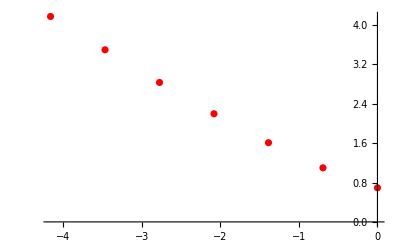

```mathematica
g1=ListPlot[b2,PlotStyle->Red]
```

```mathematica
g[x_]=Fit[b2,{1,x},x]
```

0.536438-0.848268 x

```mathematica
(* fractal dimension times series *)
```

```mathematica
d=Abs[CoefficientList[g[x],x][[2]]]
```

```mathematica
0.8482679079543909
```

```mathematica
(* conjugate fractal dimension of Farey Rational numbers*)
```

```mathematica
s0=-CoefficientList[g[x],x][[2]]
```

0.848268

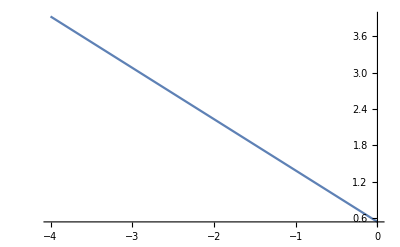

```mathematica
g2=Plot[g[x],{x,-4,0}]
```

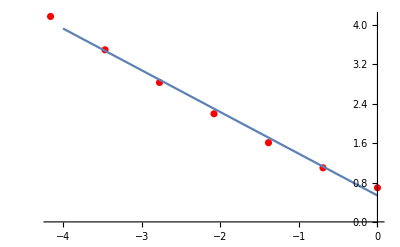

```mathematica
Show[{g1,g2}]
```

```mathematica
(* end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear [f,n,d,c,Phi,ApEn,a,i,j,k,r,m,g,digits,x,y]
```

```mathematica
(*Hyper-Farey rational function on a/b->{n,m}*)
```

```mathematica
digits=1000
```

1000

```mathematica
If[If[x>0&&x≤1/2,x/(1-x),(1-x)/x]>0&&If[x>0&&x≤1/2,x/(1-x),(1-x)/x]≤1/2,If[x>0&&x≤1/2,x/(1-x),(1-x)/x]/(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x]),(1-If[x>0&&x≤1/2,x/(1-x),(1-x)/x])/If[x>0&&x≤1/2,x/(1-x),(1-x)/x]]/.x->a/b
If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]
f[a_,b_]:=If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]
```

If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]

If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]

```mathematica
b=ParallelTable[If[n<m,N[f[n,m]],N[f[m,n]]],{n,1,digits},{m,1, digits}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Export["Hyper_Farey1000x1000_Rainbow.jpg",ListDensityPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
c=Flatten[b,1];
```

Hyper_Farey1000x1000_Rainbow.jpg

```mathematica
Export["Hyper_Farey1000x1000ArrayPlot_Rainbow.jpg",ArrayPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
```

Hyper_Farey1000x1000ArrayPlot_Rainbow.jpg

```mathematica
Length[c]
```

1000000

```mathematica
BoxCount[list_,delta0_,scale_,min_]:=Block[{tmp,delta,nmax,l,i},tmp={};
delta=delta0;
nmax=Abs[Ceiling[Log[min/delta0]/Log[scale]]];
Do[{l=Length[Complement[Ceiling[list/delta],{}]];
AppendTo[tmp,{delta,l}];
delta=delta*scale},{i,1,nmax}];
Return[tmp]];
```

```mathematica
s=Flatten[c];
```

```mathematica
Export["Hyper_Farey1000x1000Flatten_Rainbow.jpg",ListPlot[s,PlotStyle->{PointSize[0.001]},ColorFunction->"Rainbow",ImageSize->2000]]
```

Hyper_Farey1000x1000Flatten_Rainbow.jpg

```mathematica
a2=BoxCount[s,1.0,0.5,0.01]
```

{{1.,3},{0.5,4},{0.25,6},{0.125,10},{0.0625,18},{0.03125,34},{0.015625,66}}

```mathematica
b2=Table[{Log[a2[[i,1]]],N[Log[a2[[i,2]]]]},{i,Length[a2]}]
```

{{0.,1.09861},{-0.693147,1.38629},{-1.38629,1.79176},{-2.07944,2.30259},{-2.77259,2.89037},{-3.46574,3.52636},{-4.15888,4.18965}}

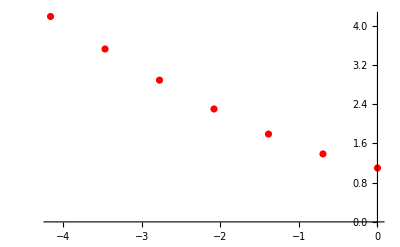

```mathematica
g1=ListPlot[b2,PlotStyle->Red]
```

```mathematica
g[x_]=Fit[b2,{1,x},x]
```

0.885248-0.754935 x

```mathematica
(* fractal dimension times series *)
```

```mathematica
d=Abs[CoefficientList[g[x],x][[2]]]
```

0.754935

```mathematica
0.8482679079543909
```

0.848268

```mathematica
(* conjugate fractal dimension of Farey Rational numbers*)
```

```mathematica
s0=-CoefficientList[g[x],x][[2]]
```

0.754935

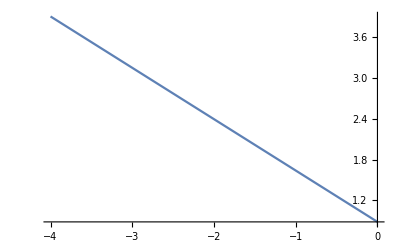

```mathematica
g2=Plot[g[x],{x,-4,0}]
```

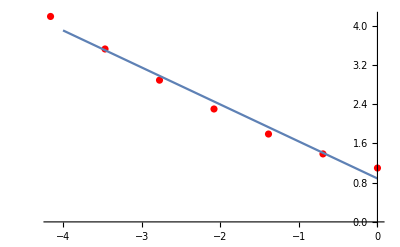

```mathematica
Show[{g1,g2}]
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear [f,n,d,c,Phi,ApEn,a,i,j,k,r,m,g,digits,x,y]
```

```mathematica
(*Hyper-Farey 2nd  rational function on a/b->{n,m}*)
```

```mathematica
digits=1000
```

1000

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

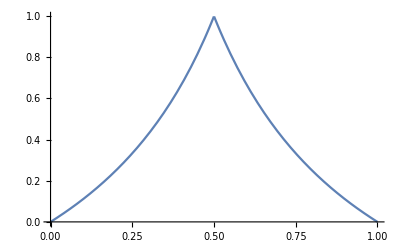

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
(*Hyper-Farey function 3rd harmonic*)
```

```mathematica
g[x_]=Nest[f,x,3];
```

```mathematica
f3[a_,b_]=g[a/b]
```

If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]

```mathematica
b=ParallelTable[If[n<m,N[f3[n,m]],N[f3[m,n]]],{n,1,digits},{m,1, digits}];
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

```mathematica
Export["Hyper_Farey2nd_1000x1000_Rainbow.jpg",ListDensityPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
c=Flatten[b,1];
```

Hyper_Farey2nd_1000x1000_Rainbow.jpg

```mathematica
Export["Hyper_Farey2nd_1000x1000ArrayPlot_Rainbow.jpg",ArrayPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
```

Hyper_Farey2nd_1000x1000ArrayPlot_Rainbow.jpg

```mathematica
Length[c]
```

1000000

```mathematica
BoxCount[list_,delta0_,scale_,min_]:=Block[{tmp,delta,nmax,l,i},tmp={};
delta=delta0;
nmax=Abs[Ceiling[Log[min/delta0]/Log[scale]]];
Do[{l=Length[Complement[Ceiling[list/delta],{}]];
AppendTo[tmp,{delta,l}];
delta=delta*scale},{i,1,nmax}];
Return[tmp]];
```

```mathematica
s=Flatten[c];
```

```mathematica
Export["Hyper_Farey2nd_1000x1000Flatten_Rainbow.jpg",ListPlot[s,PlotStyle->{PointSize[0.001]},ColorFunction->"Rainbow",ImageSize->2000]]
```

Hyper_Farey2nd_1000x1000Flatten_Rainbow.jpg

```mathematica
a2=BoxCount[s,1.0,0.5,0.01]
```

{{1.,1003},{0.5,1004},{0.25,1006},{0.125,1010},{0.0625,1018},{0.03125,1034},{0.015625,1066}}

```mathematica
b2=Table[{Log[a2[[i,1]]],N[Log[a2[[i,2]]]]},{i,Length[a2]}]
```

{{0.,6.91075},{-0.693147,6.91175},{-1.38629,6.91374},{-2.07944,6.91771},{-2.77259,6.9256},{-3.46574,6.94119},{-4.15888,6.97167}}

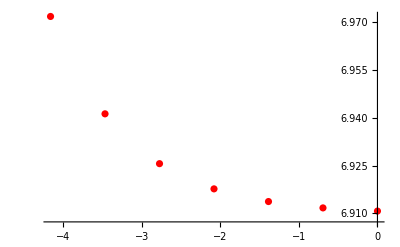

```mathematica
g1=ListPlot[b2,PlotStyle->Red]
```

```mathematica
g[x_]=Fit[b2,{1,x},x]
```

6.90032-0.0130614 x

```mathematica
(* fractal dimension times series *)
```

```mathematica
d=Abs[CoefficientList[g[x],x][[2]]]
```

0.0130614

```mathematica
(*Hyper-Farey dimension*)
0.7549351085404906
```

0.754935

```mathematica
(*Farey Dimension*)
0.8482679079543909
```

0.848268

```mathematica
(* conjugate fractal dimension of 2nd Hyoper Farey Rational numbers*)
```

```mathematica
s0=-CoefficientList[g[x],x][[2]]
```

0.0130614

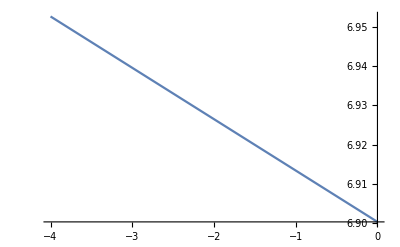

```mathematica
g2=Plot[g[x],{x,-4,0}]
```

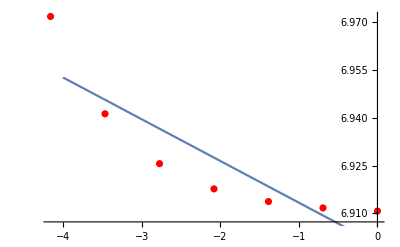

```mathematica
Show[{g1,g2}]
```

```mathematica
(* end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear [f,n,d,c,Phi,ApEn,a,i,j,k,r,m,g,digits,x,y]
```

```mathematica
(*Hyper-Farey 2nd  rational function on a/b->{n,m}*)
```

```mathematica
digits=1000
```

1000

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

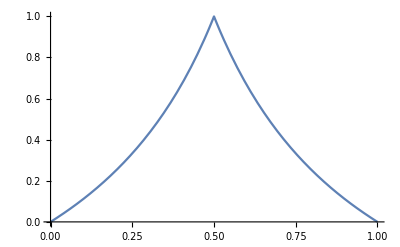

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
(*Hyper-Farey function 4th harmonic*)
```

```mathematica
g[x_]=Nest[f,x,4];
```

```mathematica
f3[a_,b_]=g[a/b]
```

If[If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]>0&&If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]≤1/2,If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]/(1-If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]),(1-If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]])/If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]]

```mathematica
b=ParallelTable[If[n<m,N[f3[n,m]],N[f3[m,n]]],{n,1,digits},{m,1, digits}];
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

```mathematica
Export["Hyper_Farey3rd_1000x1000_Rainbow.jpg",ListDensityPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
c=Flatten[b,1];
```

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Hyper_Farey3rd_1000x1000_Rainbow.jpg

```mathematica
Export["Hyper_Farey3rd_1000x1000ArrayPlot_Rainbow.jpg",ArrayPlot[b,ColorFunction->"Rainbow",ImageSize->2000]]
```

Hyper_Farey3rd_1000x1000ArrayPlot_Rainbow.jpg

```mathematica
Length[c]
```

1000000

```mathematica
BoxCount[list_,delta0_,scale_,min_]:=Block[{tmp,delta,nmax,l,i},tmp={};
delta=delta0;
nmax=Abs[Ceiling[Log[min/delta0]/Log[scale]]];
Do[{l=Length[Complement[Ceiling[list/delta],{}]];
AppendTo[tmp,{delta,l}];
delta=delta*scale},{i,1,nmax}];
Return[tmp]];
```

```mathematica
s=Flatten[c];
```

```mathematica
Export["Hyper_Farey3rd_1000x1000Flatten_Rainbow.jpg",ListPlot[s,PlotStyle->{PointSize[0.001]},ColorFunction->"Rainbow",ImageSize->2000]]
```

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Hyper_Farey3rd_1000x1000Flatten_Rainbow.jpg

```mathematica
a2=BoxCount[s,1.0,0.125,0.0001]
```

{{1.,1503},{0.125,1510},{0.015625,1566},{0.00195313,2013},{0.000244141,5487}}

```mathematica
b2=Table[{Log[a2[[i,1]]],N[Log[a2[[i,2]]]]},{i,Length[a2]}]
```

{{0.,7.31522},{-2.07944,7.31986},{-4.15888,7.35628},{-6.23832,7.60738},{-8.31777,8.61014}}

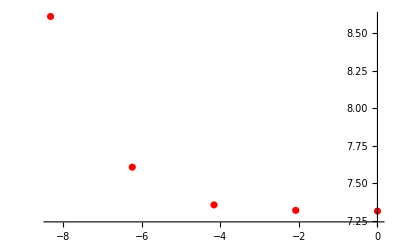

```mathematica
g1=ListPlot[b2,PlotStyle->Red]
```

```mathematica
g[x_]=Fit[b2,{1,x},x]
```

7.06631-0.138371 x

```mathematica
(* fractal dimension times series *)
```

```mathematica
d=Abs[CoefficientList[g[x],x][[2]]]
```

0.138371

```mathematica
0.013061378051410229
```

0.0130614

```mathematica
(*Hyper-Farey dimension*)
0.7549351085404906
```

0.754935

```mathematica
(*Farey Dimension*)
0.8482679079543909
```

0.848268

```mathematica
(* conjugate fractal dimension of 2nd Hyoper Farey Rational numbers*)
```

```mathematica
s0=-CoefficientList[g[x],x][[2]]
```

0.138371

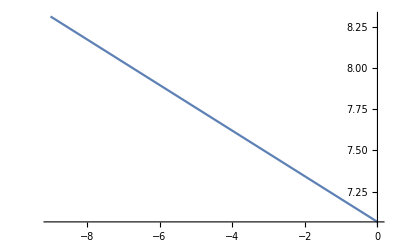

```mathematica
g2=Plot[g[x],{x,-9,0}]
```

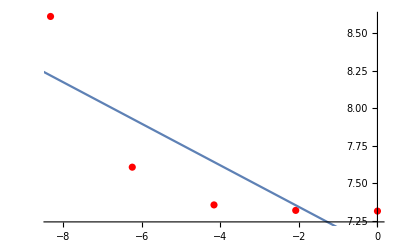

```mathematica
Show[{g1,g2}]
```

```mathematica
(* end*)
```

```mathematica
Clear[f,g,a,b]
```

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

```mathematica
(*Hyper-Farey function 4th harmonic*)
```

```mathematica
g[x_]=Nest[f,x,1];
```

```mathematica
f1[a_,b_]=f[a/b]
```

If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]

```mathematica
(*Farey  rational numbers Level 30*)
```

```mathematica
w=Flatten[Table[{a/b,f1[a,b]},{a,30},{b,30}],1];
```

```mathematica
ListPlot[w,PlotRange->All,ColorFunction->Hue]
```

```mathematica
Length[w]
```

900

```mathematica
v=Join[Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}]];
```

```mathematica
Length[v]
```

7200

```mathematica
g1=ListPointPlot3D[v,ColorFunction->"Rainbow",PlotStyle->{PointSize->Small},ImageSize->Full];
```

```mathematica
(*u=Flatten[Table[{Blue,CircleThrough[{v[[i]],v[[Length[v]+1-j]],v[[k]]}]},{i,Length[v]},{j,Length[v]},{k,Length[v]}]];
Show[Graphics[u],ImageSize->Large]*)
```

```mathematica
Clear[f,g,a,b,w,v]
```

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

```mathematica
(*Hyper-Farey function 4th harmonic*)
```

```mathematica
g[x_]=Nest[f,x,1];
```

```mathematica
f1[a_,b_]=f[f[a/b]]
```

If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]

```mathematica
(*Hyper-Farey  rational numbers Level 30*)
```

```mathematica
w=Flatten[Table[{a/b,f1[a,b]},{a,30},{b,30}],1];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ListPlot[w,PlotRange->All,ColorFunction->Hue]
```

```mathematica
Length[w]
```

900

```mathematica
v=Join[Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}]];
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Length[v]
```

7200

```mathematica
g2=ListPointPlot3D[v,ColorFunction->"Rainbow",PlotStyle->{PointSize->Small},ImageSize->Full];
```

```mathematica
Clear[f,g,a,b]
```

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

```mathematica
(*Hyper-Farey function  harmonic*)
```

```mathematica
g[x_]=Nest[f,x,1];
```

```mathematica
f1[a_,b_]=f[f[f[a/b]]]
```

If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]

```mathematica
(*Farey  rational numbers Level 30*)
```

```mathematica
w=Flatten[Table[{a/b,f1[a,b]},{a,30},{b,30}],1];
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

```mathematica
ListPlot[w,PlotRange->All,ColorFunction->Hue]
```

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

```mathematica
Length[w]
```

900

```mathematica
v=Join[Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}]];
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Length[v]
```

7200

```mathematica
g3=ListPointPlot3D[v,ColorFunction->"Rainbow",PlotStyle->{PointSize->Small},ImageSize->Full];
```

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

```mathematica
Clear[f,g,a,b]
```

```mathematica
f[x_]=If[x>0&&x<=1/2,(x/(1-x)),((1-x)/x)]
```

If[x>0&&x≤1/2,x/(1-x),(1-x)/x]

```mathematica
(*Hyper-Farey function  harmonic*)
```

```mathematica
g[x_]=Nest[f,x,1];
```

```mathematica
f1[a_,b_]=f[f[f[f[a/b]]]]
```

If[If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]>0&&If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]≤1/2,If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]/(1-If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]),(1-If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]])/If[If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]>0&&If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]≤1/2,If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]/(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]),(1-If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]])/If[If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]>0&&If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]≤1/2,If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]/(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]),(1-If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)])/If[a/b>0&&a/b≤1/2,a/(b (1-a/b)),(1-a/b)/(a/b)]]]]

```mathematica
(*hyper-Farey 3rd  rational numbers Level 30*)
```

```mathematica
w=Flatten[Table[{a/b,f1[a,b]},{a,30},{b,30}],1];
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

```mathematica
ListPlot[w,PlotRange->All,ColorFunction->Hue]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

```mathematica
Length[w]
```

900

```mathematica
v=Join[Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],Table[-{-2*w[[i,1]]/(1+w[[i]].w[[i]]),2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}],
Table[-{2*w[[i,1]]/(1+w[[i]].w[[i]]),-2*w[[i,2]]/(1+w[[i]].w[[i]]),-(1-w[[i]].w[[i]])/(1+w[[i]].w[[i]])},{i,Length[w]}]];
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Length[v]
```

7200

```mathematica
g4=ListPointPlot3D[v,ColorFunction->"Rainbow",PlotStyle->{PointSize->Small},ImageSize->Full];
```

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

```mathematica
Export["Farey_Harmonics_4th_Octant_Gauss_map.jpg",GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->{4000,4000}]]
```

Farey_Harmonics_4th_level.jpg